### Products of operators

Use the Virasoro algebra to reorder products of L in ascending order:

```mathematica
SetAttributes[CircleTimes,Flat]
```

```mathematica
CircleTimes/:CircleTimes[x___,L[m_],L[n_],y___]:=CircleTimes[x,L[n],L[m],y]+(m-n)CircleTimes[x,L[m+n],y]-c/12 n(n-1)(n+1)KroneckerDelta[m+n,0]CircleTimes[x,y]/;n<m
```

L_m with m>=-1 annihilate the vacuum state Ω

```mathematica
CircleTimes/:CircleTimes[x___,L[m_],Ω]:=0/;m>=-1
CircleTimes/:CircleTimes[Ω,L[m_],x___]:=0/;m<=1
```

```mathematica
CircleTimes/:CircleTimes[x___,y1_+y2_,z___]:=CircleTimes[x,y1,z]+CircleTimes[x,y2,z]
```

```mathematica
CircleTimes/:CircleTimes[x___,n_ y_,z___]:=n CircleTimes[x,y,z]/;FreeQ[n,L]&&FreeQ[n,ϕ]
```

```mathematica
CircleTimes/:CircleTimes[x___,1,y__]:=CircleTimes[x,y]
CircleTimes/:CircleTimes[x__,1,y___]:=CircleTimes[x,y]
```

```mathematica
CircleTimes/:CircleTimes[Ω,Ω]:=1
```

```mathematica
(*CircleTimes/:CircleTimes[ϕϕ[n_],L[m_],x___]:=(h+s n+e)(a m+n f+b) CircleTimes[ϕϕ[n+m],x]
(*CircleTimes/:CircleTimes[ϕϕ[0],Ω]:=1*)*)
```

Commutation with a local operator ϕ:
	[L_n,ϕ(z)]=z^(n+1)∂/(∂z)ϕ(z)+h(n+1)z^n ϕ(z)
	[L_n,∂^m/(∂z^m)ϕ(z)]=∂^m/(∂z^m)(z^(n+1)∂/(∂z)ϕ(z)+h(n+1)z^n ϕ(z))
	=∑_(i=0)^m (m!)/(i!(m-i)!)((∂^i/(∂z^i)z^(n+1))∂^(m-i+1)/(∂z^(m-i+1))ϕ(z)+h(n+1)(∂^i/(∂z^i)z^n)∂^(m-i)/(∂z^(m-i))ϕ(z))

```mathematica
CircleTimes/:CircleTimes[x___,ϕ[z_],L[n_],y___]:=CircleTimes[x,L[n],ϕ[z],y]-z^(n+1) CircleTimes[x,ϕ'[z],y]-h(n+1)z^n CircleTimes[x,ϕ[z],y]
CircleTimes/:CircleTimes[x___,Derivative[m_][ϕ][z_],L[n_],y___]:=CircleTimes[x,L[n],Derivative[m][ϕ][z],y]-∑_(i=0)^m (m!)/(i!(m-i)!)(D[z^(n+1),{z,i}] CircleTimes[x,Derivative[m-i+1][ϕ][z],y]+h(n+1)D[z^n,{z,i}]CircleTimes[x,Derivative[m-i][ϕ][z],y])
```

```mathematica
(*CircleTimes/:CircleTimes[x___,zdϕ[a_,b_],L[n_],y___]:=CircleTimes[x,L[n],zdϕ[a,b],y]-(h-a+b)(n+1)CircleTimes[x,zdϕ[a+n,b],y]-CircleTimes[x,zdϕ[a+n+1,b+1],y]*)
```

```mathematica
(*CircleTimes/:CircleTimes[Ω,zdϕ[a1_,b1_],zdϕ[a2_,b2_],Ω]:=z1^a1 z2^a2 D[1/(z1-z2)^(2h),{z1,b1},{z2,b2}]*)
```

```mathematica
CircleTimes/:CircleTimes[Ω,ϕ[z1_],ϕ[z2_],Ω]:=1/(z1-z2)^(2h)
CircleTimes/:CircleTimes[Ω,Derivative[m_][ϕ][z1_],ϕ[z2_],Ω]:=D[1/(z1-z2)^(2h),{z1,m}]
CircleTimes/:CircleTimes[Ω,ϕ[z1_],Derivative[m_][ϕ][z2_],Ω]:=D[1/(z1-z2)^(2h),{z2,m}]
CircleTimes/:CircleTimes[Ω,Derivative[m1_][ϕ][z1_],Derivative[m2_][ϕ][z2_],Ω]:=D[1/(z1-z2)^(2h),{z1,m1},{z2,m2}]
```

```mathematica
ϕϕ[z1_,z2_,n_]:=1/((z1-z2)^(2h-n)z1^n z2^n)
```

Hermitian conjugation:

```mathematica
SuperDagger/:SuperDagger[CircleTimes[ops__]]:=CircleTimes@@Reverse[Map[SuperDagger,{ops}]]
```

```mathematica
SuperDagger/:SuperDagger[L[m_]]:=L[-m]
SuperDagger/:SuperDagger[n_ x_]:=n SuperDagger[x]/;FreeQ[n,L]
SuperDagger/:SuperDagger[Ω]:=Ω
SuperDagger/:SuperDagger[x_+y_]:=SuperDagger[x]+SuperDagger[y]
```

## Computation

### Level 2

```mathematica
ψ2=L[-2]⊗Ω
```

L[-2]⊗Ω

```mathematica
L[1]⊗ψ2
```

0

```mathematica
N2=SuperDagger[ψ2]⊗ψ2
```

c/2

```mathematica
C2[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ2)/ϕϕ[z1,z2,2]//Simplify
```

h

```mathematica
C2[c_,h_]=C2[h]^2/N2//Factor
```

(2 h^2)/c

#### Level 3

```mathematica
ψ3ansatz=L[-3]⊗Ω;
```

```mathematica
L[1]⊗ψ3ansatz
```

4 L[-2]⊗Ω

### Level 4

```mathematica
ψ4ansatz=(c1 L[-2]⊗L[-2]+c2  L[-4])⊗Ω;
```

```mathematica
L[1]⊗ψ4ansatz//Simplify
```

(3 c1+5 c2) L[-3]⊗Ω

```mathematica
ψ4=(L[-2]⊗L[-2]-3/5  L[-4])⊗Ω;
```

```mathematica
L[1]⊗ψ4//Simplify
```

0

```mathematica
N4=SuperDagger[ψ4]⊗ψ4//Factor
```

1/10 c (22+5 c)

```mathematica
C4[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ4)/ϕϕ[z1,z2,4]//Factor
```

1/5 h (1+5 h)

```mathematica
C4[c_,h_]=C4[h]^2/N4//Factor
```

(2 h^2 (1+5 h)^2)/(5 c (22+5 c))

### Level 5

```mathematica
ψ5ansatz=(c1  L[-5]+c2 L[-3]⊗L[-2])⊗Ω;
```

```mathematica
L[1]⊗ψ5ansatz//Simplify
```

6 c1 L[-4]⊗Ω+4 c2 L[-2]⊗L[-2]⊗Ω

### Level 6

```mathematica
ψ6ansatz=(c1 L[-6]+c2 L[-4]⊗L[-2]+c3 L[-3]⊗L[-3]+c4 L[-2]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
L[1]⊗ψ6ansatz//Simplify
```

(7 c1+4 c3+6 c4) L[-5]⊗Ω+(5 c2+8 c3+9 c4) L[-3]⊗L[-2]⊗Ω

```mathematica
ψ6a=(-20/63 L[-6]
-8/9 L[-4]⊗L[-2]
+5/9 L[-3]⊗L[-3])⊗Ω;
ψ6b=(-(60c+78)/(70c+29)L[-6]
-(3(42c+67))/(70c+29)L[-4]⊗L[-2]
+93/(70c+29)L[-3]⊗L[-3]
+L[-2]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
L[1]⊗ψ6a//Simplify
L[1]⊗ψ6b//Simplify
```

0

0

```mathematica
SuperDagger[ψ6a]⊗ψ6b//Simplify
```

0

```mathematica
N6a=SuperDagger[ψ6a]⊗ψ6a//Factor
N6b=SuperDagger[ψ6b]⊗ψ6b//Factor
```

4/63 c (29+70 c)

(3 c (-1+2 c) (22+5 c) (68+7 c))/(4 (29+70 c))

```mathematica
C6a[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ6a)/ϕϕ[z1,z2,6]//Factor
C6b[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ6b)/ϕϕ[z1,z2,6]//Factor
```

-2/63 h (1+14 h)

(h (-2+8 c-57 h+42 c h+29 h^2+70 c h^2))/(29+70 c)

```mathematica
C6[c_,h_]=C6a[h]^2/N6a+C6b[h]^2/N6b//Factor
```

(h^2 (-40+90 c+c^2-784 h+1176 c h+28 c^2 h-1036 h^2+6048 c h^2+196 c^2 h^2-9576 h^3+7056 c h^3+2436 h^4+5880 c h^4))/(63 c (-1+2 c) (22+5 c) (68+7 c))

### Level 7

```mathematica
ψ7ansatz=(c1 L[-7]+c2 L[-5]⊗L[-2]+c3 L[-4]⊗L[-3]+c4 L[-3]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
L[1]⊗ψ7ansatz//Simplify
```

8 c1 L[-6]⊗Ω+(6 c2+4 c3) L[-4]⊗L[-2]⊗Ω+5 c3 L[-3]⊗L[-3]⊗Ω+3 c4 L[-3]⊗L[-3]⊗Ω+4 c4 L[-2]⊗L[-2]⊗L[-2]⊗Ω

### Level 8

```mathematica
ψ8ansatz=(c1 L[-8]+c2 L[-6]⊗L[-2]+c3 L[-5]⊗L[-3]+c4 L[-4]⊗L[-4]+c5 L[-4]⊗L[-2]⊗L[-2]+c6 L[-3]⊗L[-3]⊗L[-2]+c7 L[-2]⊗L[-2]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
Collect[L[1]⊗ψ8ansatz,CircleTimes[__],Simplify]
```

(9 c1+5 c4+27 c7) L[-7]⊗Ω+(7 c2+4 (c3+c6+6 c7)) L[-5]⊗L[-2]⊗Ω+(6 c3+10 c4+3 c5) L[-4]⊗L[-3]⊗Ω+(5 c5+8 c6+18 c7) L[-3]⊗L[-2]⊗L[-2]⊗Ω

```mathematica
ψ8a=(
35L[-8]-60 L[-6]⊗L[-2]
+105 L[-5]⊗L[-3]-63L[-4]⊗L[-4])⊗Ω;
ψ8b=(
(83+140 c)(10L[-8]-18 L[-4]⊗L[-4])
+60(-19+5 c) L[-6]⊗L[-2]
+10(227+210 c) L[-5]⊗L[-3]
+5(11+105 c)(8L[-4]⊗L[-2]⊗L[-2]-5L[-3]⊗L[-3]⊗L[-2]))⊗Ω;
ψ8c=(6 (-543+2315 c+630 c^2) L[-8]
+24 (67+569 c+150 c^2) L[-6]⊗L[-2]
+12 (-487+126 c) L[-5]⊗L[-3]
-27 (-167+265 c+42 c^2) L[-4]⊗L[-4]
+6 (-557+3471 c+630 c^2) L[-4]⊗L[-2]⊗L[-2]
-12 (-127+465 c) L[-3]⊗L[-3]⊗L[-2]
-(-251+3305 c+1050 c^2)L[-2]⊗L[-2]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
L[1]⊗ψ8a//Simplify
L[1]⊗ψ8b//Simplify
L[1]⊗ψ8c//Simplify
```

0

0

0

```mathematica
SuperDagger[ψ8a]⊗ψ8b//Simplify
SuperDagger[ψ8a]⊗ψ8c//Simplify
SuperDagger[ψ8b]⊗ψ8c//Simplify
```

0

0

0

```mathematica
N8a=SuperDagger[ψ8a]⊗ψ8a//Factor
N8b=SuperDagger[ψ8b]⊗ψ8b//Factor
N8c=SuperDagger[ψ8c]⊗ψ8c//Factor
```

4290 c (11+105 c)

130 c (22+5 c) (11+105 c) (-251+3305 c+1050 c^2)

3/2 c (-1+2 c) (46+3 c) (3+5 c) (22+5 c) (68+7 c) (-251+3305 c+1050 c^2)

```mathematica
C8a[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ8a)/ϕϕ[z1,z2,8]//Factor
C8b[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ8b)/ϕϕ[z1,z2,8]//Factor
C8c[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ8c)/ϕϕ[z1,z2,8]//Factor
```

-h (1+27 h)

2 h (-4+55 c-218 h+435 c h+110 h^2+1050 c h^2)

-h (-6+78 c+108 c^2-829 h-701 c h+606 c^2 h+918 h^2-498 c h^2+1260 c^2 h^2-251 h^3+3305 c h^3+1050 c^2 h^3)

```mathematica
C8[c_,h_]=C8a[h]^2/N8a+C8b[h]^2/N8b+C8c[h]^2/N8c//Factor;
```

### Level 10

```mathematica
ψ10ansatz=(c1 L[-10]+c2 L[-8]⊗L[-2]+c3 L[-7]⊗L[-3]+c4 L[-6]⊗L[-4]+c5 L[-5]⊗L[-5]+c6 L[-6]⊗L[-2]⊗L[-2]+c7 L[-5]⊗L[-3]⊗L[-2]+c8 L[-4]⊗L[-4]⊗L[-2]+c9 L[-4]⊗L[-3]⊗L[-3]+c10 L[-4]⊗L[-2]⊗L[-2]⊗L[-2]+c11 L[-3]⊗L[-3]⊗L[-2]⊗L[-2]+c12 L[-2]⊗L[-2]⊗L[-2]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
Collect[L[1]⊗ψ10ansatz,CircleTimes[__],Simplify]
```

(11 c1+6 c10+180 c12+6 c5+4 c9) L[-9]⊗Ω+(135 c12+9 c2+4 c3+5 c8) L[-7]⊗L[-2]⊗Ω+(8 c3+5 c4+3 c6) L[-6]⊗L[-3]⊗Ω+(6 c10+7 c4+4 (3 c5+c9)) L[-5]⊗L[-4]⊗Ω+(4 c11+60 c12+7 c6+4 c7) L[-5]⊗L[-2]⊗L[-2]⊗Ω+(9 c10+6 c7+10 c8+8 c9) L[-4]⊗L[-3]⊗L[-2]⊗Ω+(3 c11+5 c9) L[-3]⊗L[-3]⊗L[-3]⊗Ω+(5 c10+8 c11+30 c12) L[-3]⊗L[-2]⊗L[-2]⊗L[-2]⊗Ω

```mathematica
ψ10a=(252L[-10]+220 L[-8]⊗L[-2]
-495 L[-7]⊗L[-3]+792L[-6]⊗L[-4]-462 L[-5]⊗L[-5])⊗Ω;
ψ10b=(
(143+420 c)(42 L[-10]+132 L[-6]⊗L[-4]-77 L[-5]⊗L[-5])
+315 (19+110 c) L[-8]⊗L[-2]
-105 (106+165 c)L[-7]⊗L[-3]
+(89+2310 c)(-20 L[-6]⊗L[-2]⊗L[-2]+35 L[-5]⊗L[-3]⊗L[-2]-21 L[-4]⊗L[-4]⊗L[-2]))⊗Ω;
ψ10c=(-12 (12389+12523 c+30870 c^2) L[-10]
+4 (-48371+408390 c+123200 c^2) L[-8]⊗L[-2]
+6 (44469+57035 c+57750 c^2) L[-7]⊗L[-3]
-12 (40599-40417 c+39270 c^2) L[-6]⊗L[-4]
-4 (-73957+210336 c+32340 c^2) L[-5]⊗L[-5]
-4 (-25119+430225 c+34650 c^2) L[-6]⊗L[-2]⊗L[-2]
+4 (-46867+892500 c+161700 c^2) L[-5]⊗L[-3]⊗L[-2]
-84 (-1605+38264 c+13860 c^2) L[-4]⊗L[-4]⊗L[-2]+(-2327+111685 c+80850 c^2)(3L[-4]⊗L[-3]⊗L[-3]+8 L[-4]⊗L[-2]⊗L[-2]⊗L[-2]-5L[-3]⊗L[-3]⊗L[-2]⊗L[-2]))⊗Ω;
ψ10d=(-504 (266+1693 c+300 c^2) L[-10]
-6 (41983+253325 c+34650 c^2) L[-8]⊗L[-2]
-36 (-4358+3225 c) L[-7]⊗L[-3]
+36 (-8405+16783 c+1650 c^2) L[-6]⊗L[-4]
+12 (18353+2586 c) L[-5]⊗L[-5]
-12 (-7161+58115 c+8250 c^2) L[-6]⊗L[-2]⊗L[-2]
-924 (259+90 c) L[-5]⊗L[-3]⊗L[-2]
+9 (25133+84285 c+6930 c^2) L[-4]⊗L[-4]⊗L[-2]
-6 (1081+5115 c)(3 L[-4]⊗L[-3]⊗L[-3]-5 L[-3]⊗L[-3]⊗L[-2]⊗L[-2])
-30 (2483+23519 c+2310 c^2) L[-4]⊗L[-2]⊗L[-2]⊗L[-2]
+(3767+76675 c+11550 c^2)L[-2]⊗L[-2]⊗L[-2]⊗L[-2]⊗L[-2])⊗Ω;
```

```mathematica
L[1]⊗ψ10a//Simplify
L[1]⊗ψ10b//Simplify
L[1]⊗ψ10c//Simplify
L[1]⊗ψ10d//Simplify
```

0

0

0

«1 more identical outputs»

```mathematica
SuperDagger[ψ10a]⊗ψ10b//Simplify
SuperDagger[ψ10a]⊗ψ10c//Simplify
SuperDagger[ψ10a]⊗ψ10d//Simplify
SuperDagger[ψ10b]⊗ψ10c//Simplify
SuperDagger[ψ10b]⊗ψ10d//Simplify
SuperDagger[ψ10c]⊗ψ10d//Simplify
```

0

0

0

«3 more identical outputs»

```mathematica
N10a=SuperDagger[ψ10a]⊗ψ10a//Factor
N10b=SuperDagger[ψ10b]⊗ψ10b//Factor
N10c=SuperDagger[ψ10c]⊗ψ10c//Factor
N10d=SuperDagger[ψ10d]⊗ψ10d//Factor
```

48620 c (89+2310 c)

153 c (22+5 c) (89+2310 c) (-2327+111685 c+80850 c^2)

34 c (-1+2 c) (22+5 c) (68+7 c) (3767+76675 c+11550 c^2) (-2327+111685 c+80850 c^2)

15/4 c (-1+2 c) (46+3 c) (3+5 c) (22+5 c) (68+7 c) (232+11 c) (3767+76675 c+11550 c^2)

```mathematica
C10a[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ10a)/ϕϕ[z1,z2,10]//Factor
C10b[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ10b)/ϕϕ[z1,z2,10]//Factor
C10c[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ10c)/ϕϕ[z1,z2,10]//Factor
C10d[h_]=(Ω⊗ϕ[z1]⊗ϕ[z2]⊗ψ10d)/ϕϕ[z1,z2,10]//Factor
```

2 h (1+44 h)

-9 h (-2+70 c-177 h+770 c h+89 h^2+2310 c h^2)

2 h (-74+486 c+8540 c^2-15857 h-71659 c h+59290 c^2 h+17255 h^2-130327 c h^2+154770 c^2 h^2-4654 h^3+223370 c h^3+161700 c^2 h^3)

h (-24+1608 c+1440 c^2-16342 h-10898 c h+8580 c^2 h+29929 h^2-25615 c h^2+20130 c^2 h^2-18410 h^3+30590 c h^3+23100 c^2 h^3+3767 h^4+76675 c h^4+11550 c^2 h^4)

```mathematica
C10[c_,h_]=C10a[h]^2/N10a+C10b[h]^2/N10b+C10c[h]^2/N10c+C10d[h]^2/N10d//Factor;
```

### Special value of c

```mathematica
2c C2[c,h]
```

4 h^2

```mathematica
2c C4[c,h]/.{c->(12h (h+2))/(20 h^2+1)-2}//Simplify
```

1/15 h^2 (1+20 h^2)

```mathematica
2c C6[c,h]/.{c->(12h (h+2))/(20 h^2+1)-2}//Factor
```

(h^2 (1+20 h^2) (-18+64 h+91 h^2+2422 h^3+8652 h^4+3864 h^5))/(189 (-5+38 h) (9+28 h+194 h^2))

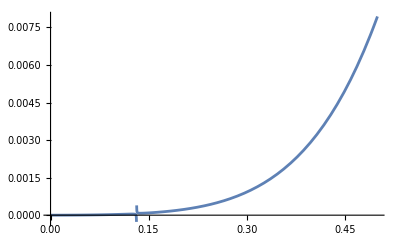

```mathematica
Plot[%,{h,0,1/2}]
```

```mathematica
2c C8[c,h]/.{c->(12h (h+2))/(20 h^2+1)-2}//Factor
```

-((h^2 (1+20 h^2) (2700-49020 h+94731 h^2-858724 h^3+5518907 h^4+37027334 h^5+119002584 h^6+646203888 h^7+292386864 h^8+510952288 h^9-1269931520 h^10+430144000 h^11))/(10296 (-5+38 h) (7-120 h+80 h^2) (9+28 h+194 h^2) (10+18 h+209 h^2)))

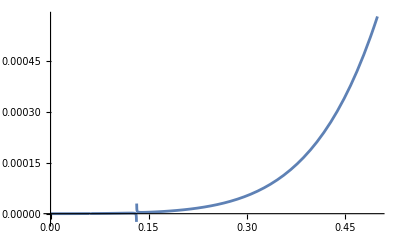

```mathematica
Plot[%,{h,0,1/2}]
```

```mathematica
2c C10[c,h]/.{c->(12h (h+2))/(20 h^2+1)-2}//Factor//InputForm
```

-1/2625480*(h^2*(1 + 20*h^2)*(1058400 - 17256960*h + 
    21319236*h^2 - 618518876*h^3 + 1514275529*h^4 + 
    15251568716*h^5 + 100079803869*h^6 + 786358489906*h^7 + 
    1752864090076*h^8 + 7985264000824*h^9 + 
    7098931393840*h^10 + 12629380947040*h^11 - 
    11847773995200*h^12 - 5641900950400*h^13 - 
    683947264000*h^14 + 4197656320000*h^15))/
  ((-5 + 38*h)*(7 - 120*h + 80*h^2)*(9 + 28*h + 194*h^2)*
   (10 + 18*h + 209*h^2)*(35 + 44*h + 722*h^2))

### 4-state Potts model

```mathematica
{C2[1,1/4],C4[1,1/4],C6[1,1/4],C8[1,1/4],C10[1,1/4]}
```

{1/8,3/640,5/21504,175/14057472,441/637272064}

```mathematica
Table[Gamma[2h]/Gamma[h]^2,{h,2,10,2}]%
%//N
```

{3/4,21/32,165/256,2625/4096,41895/65536}

{0.75,0.65625,0.644531,0.640869,0.639267}

### Free fermion

```mathematica
Series[C6[c,h],{h,1/2,1}]//FullSimplify
```

(6943+128 c)/(1008 c (22+5 c) (68+7 c))+((4909+80 c) (h-1/2))/(84 c (22+5 c) (68+7 c))+O[h-1/2]^2

```mathematica
Limit[C6[c,1/2],c->1/2]//Simplify
```

1/126

```mathematica
(6943+128 c)/(1008 c (22+5 c) (68+7 c))
```

```mathematica
{C2[1/2,1/2],C4[1/2,1/2],Limit[C6[c,1/2],c->1/2],Limit[C8[c,1/2],c->1/2],Limit[C10[c,1/2],c->1/2]}
```

{1,1/10,1/126,1/1716,1/24310}

### c=1

```mathematica
C2[1,h]
```

2 h^2

```mathematica
C4[1,h]
```

2/135 h^2 (1+5 h)^2

```mathematica
C6[1,h]//Factor
```

(h^2 (17+140 h+1736 h^2-840 h^3+2772 h^4))/42525

```mathematica
C8[1,h]//Factor
```

1/227026800 h^2 (3375+21210 h+490231 h^2+198000 h^3+510048 h^4+640640 h^5+782496 h^6)